# Script for IRS vs BoB comparison 1:1 Mass ratio

## to accompany https://arxiv.org/abs/2205.14742

Author: Maria Babiuc-Hamilton and Dillon Buskirk

```mathematica
ClearAll["Global`*"];Off[General::spell];Remove["Global`*"]
SetOptions[Simplify,TimeConstraint->1000];
$Assumptions=η>0 &&t∈Reals;
Unprotect[Sqrt]; Sqrt[x_^2]:=x; Protect[Sqrt];
$MinPrecision=$MachinePrecision; (* $MachinePrecision;*)
```

Initial and final parameters

From FinalSpinMassQNM.nb,  values for equal non-spinning binaries χf0Meq and Mfχ0Meq

```mathematica
χf=0.686526691452522(*mean final spin for nonspinning individual BSs in the binary *)
```

0.686527

```mathematica
Mf=0.9512489937499999(*mean final mass for nonspinning individual BSs in the binary *)
```

0.951249

Our fit: the mean value for equal non-spinning binaries from FinalSpinMassQNM.nb,  for l=2, m=2 mode:

```mathematica
MfωQNM =0.529310842319632
QQNM=3.230967016417037
ωQNM=MfωQNM/Mf
τ = 2 QQNM/ωQNM(*15.144152677226*)
```

0.529311

3.23097

0.556438

11.613

McWilliams fits

```mathematica
ωisco=(-0.091933*χf+0.097593)/(χf^2-2.4228*χf+1.4366)
ωqnm=1.5251-1.1568*(1-χf)^0.1292
```

0.140958

0.529311

PN fits

```mathematica
rISCO = 3.45425
```

3.45425

```mathematica
MωISCO = Simplify[1/(rISCO^(3/2)+χf)]
```

0.140717

Freely chosen parameters

```mathematica
Ap=1;R=1;tp=0;
```

Starting BOB formulation

take the initial values from the i3PN nspiral for ti = tISCO = tLR

Values taken directly from EccInsMerger_q1e0001. For this spin, rISCO=3.45425.

```mathematica
Ω3OrbPNISCO = 0.075297 ;
Ω3OrbPNISCOdot = 8.57723 10^-4 ;
```

Now we can implement the BoB

```mathematica
Ωi =Ω3OrbPNISCO;
Ωidot = Ω3OrbPNISCOdot;
tp =0;
ΩQNM=ωQNM/2
ti=tp-τ/2 Log[(ΩQNM^4-Ωi^4)/(2*τ*Ωi^3 Ωidot)-1]
```

0.278219

-38.0368

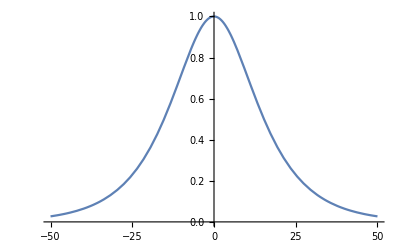

```mathematica
Ap=1;(*1.068*(1-Mf)^0.8918;*)
ψ4[t_]:=Ap*Sech[(t-tp)/τ];
Plot[ψ4[t],{t,-50,50}]
```

```mathematica
kB=((ΩQNM^4-Ωi^4)/(1-Tanh[(ti-tp)/τ]))
```

0.00298401

```mathematica
ΩB[t_]:=(Ωi^4+kB(Tanh[(t-tp)/τ]-Tanh[(ti-tp)/τ]))^(1/4)
```

```mathematica
ωBoB[t_]:=2*ΩB[t];
```

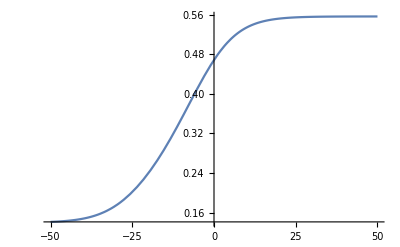

```mathematica
Plot[ωBoB[t],{t,-50,50}]
```

```mathematica
Kappap=(Ωi^4+kB(1-Tanh[(ti-tp)/τ]))^(1/4)
```

0.278219

```mathematica
Kappam=(Ωi^4-kB(1+Tanh[(ti-tp)/τ]))^(1/4)
```

0.0697199

```mathematica
arctanp[t_]:=Kappap*τ*(ArcTan[(ΩB[t]/Kappap)]-ArcTan[Ωi/Kappap])
arctanm[t_]:=Kappam*τ*(ArcTan[ΩB[t]/Kappam]-ArcTan[Ωi/Kappam])
arctanhp[t_]:=Kappap*τ*(ArcTanh[ΩB[t]/Kappap]-ArcTanh[Ωi/Kappap])
arctanhm[t_]:=Kappam*τ*(ArcTanh[ΩB[t]/Kappam]-ArcTanh[Ωi/Kappam])
```

```mathematica
PhaseB[t_]:=arctanp[t]+arctanhp[t]-arctanm[t]-arctanhm[t]
```

```mathematica
ϕBoB[t_]:=2*PhaseB[t]
```

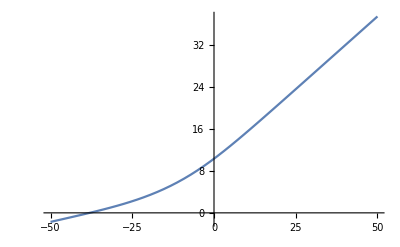

```mathematica
Plot[ϕBoB[t],{t,-50,50}]
```

```mathematica
AmpBoB[t_]:=ψ4[t]/ωBoB[t]^2
```

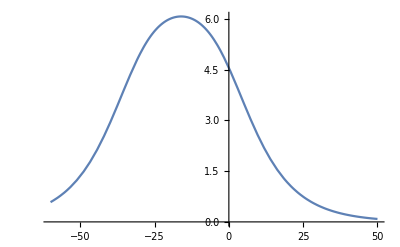

```mathematica
Plot[AmpBoB[t],{t,-60,50}]
```

```mathematica
MaxAmpBoB=FindMaxValue[{AmpBoB[t],-40<=t<=0},{t,-20}]
```

6.0778

```mathematica
tpBoB = First@FindArgMax[{AmpBoB[t],-40<=t<=0},{t,-20}]
```

-16.0715

```mathematica
hBoB[t_]:=-AmpBoB[t]*Exp[-ⅈ* ϕBoB[t]]
```

Note that the maximum in amplitude and maximum in the rate of variation of the frequency is not the same!

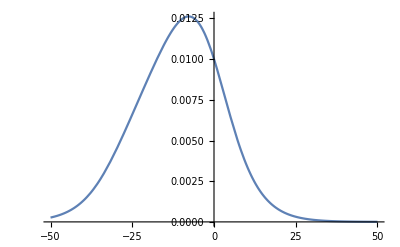

```mathematica
Plot[ωBoB'[t],{t,-50,50}]
```

```mathematica
tfBoB=t/.FindRoot[ωBoB''[t]==0,{t,-20,10}]
```

-7.73417

Now we implement the IRS

```mathematica
m1 =0.5; m2=1-m1;
q=m1/m2; M=m1+m2; μ=(m1*m2)/M;η=μ/M;
```

Check the initial frequency, quality factor and damping time against the numerical fit

```mathematica
sfn=χf
ωqnm=1-0.63(1-sfn)^0.3
```

0.686527

0.555163

```mathematica
ScientificForm[MeanDeviation[{ωqnm,ωQNM}]]
```

6.37277×10^-4

```mathematica
Q=2/(1-sfn)^0.45;
```

```mathematica
ScientificForm[MeanDeviation[{Q,QQNM}]]
```

6.99427×10^-2

```mathematica
b=N[16014/979-29132/1343 η^2]
```

15.0018

1107.1181 takes b = τ

Will use ωQNM, τ  and QQNM for consistency

```mathematica
c=N[206/903+180/1141 η^(1/2)+424/1205*η^2/Log[η]]
kI=N[713/1056-23/193 η]
α=N[1/QQNM^2(16313/562+21345/124 η)]
```

0.291143

0.645397

6.90295

```mathematica
fs[t_]:=c/2(1+1/kI)^(1+kI)(1-(1+1/kI ⅇ^((-2*t)/τ))^-kI);
fs2=Simplify[fs[t]^2, Assumptions->{η>0}];fs4=Simplify[fs2^2];
fsdot=Simplify[D[fs[t],t]];
```

```mathematica
fs[50]
```

0.000123601

```mathematica
ωIRS[t_]:=2*ΩQNM*(1-fs[t])
```

```mathematica
ωIRS[t]/.{t->50}
```

0.556369

```mathematica
ωQNM
```

0.556438

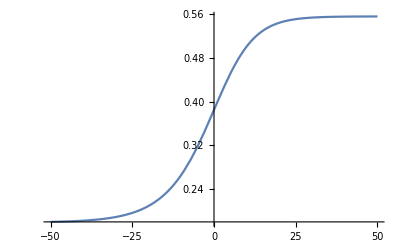

```mathematica
Plot[ωIRS[t],{t,-50,50}]
```

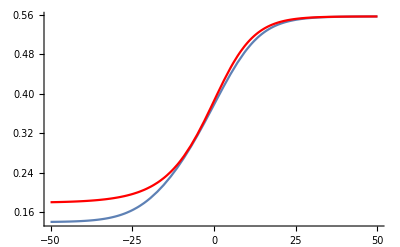

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[ωIRS[t],{t,-50,50},PlotStyle->Red], Axes->True,AxesOrigin->Automatic, PlotRange->{0,All}]
```

Initial values don’t match

```mathematica
ωIRS[ti]
```

0.182795

```mathematica
ωBoB[ti+tfBoB]
```

0.142648

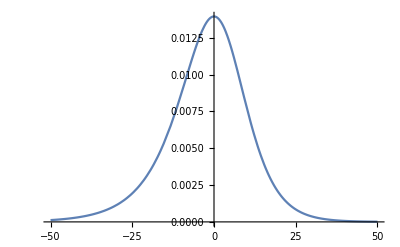

```mathematica
Plot[ωIRS'[t],{t,-50,50}]
```

```mathematica
tfIRS=t/.FindRoot[ωIRS''[t]==0,{t,-40,40}]
```

-8.36902×10^-16

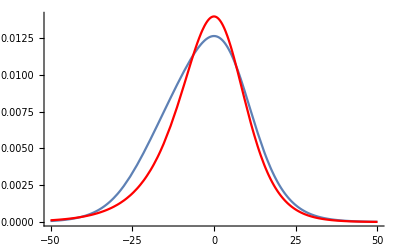

```mathematica
Show[Plot[ωBoB'[t+tfBoB],{t,-50,50}],
Plot[ωIRS'[t+tfIRS],{t,-50,50},PlotStyle->Red], Axes->True,AxesOrigin->Automatic, PlotRange->{0,All}]
```

```mathematica
ϕIRS= Integrate[ωIRS[t],t];
```

```mathematica
Δϕ= Re[ϕBoB[tfBoB]] - Simplify[ϕIRS/.{t->0}]
```

4.82193

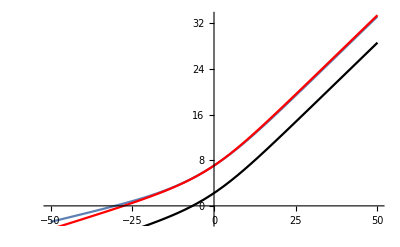

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],
Plot[ϕIRS,{t,-50,50},PlotStyle->Black]]
```

```mathematica
AmpIRS[t_]:=Simplify[Ap/ωIRS[t](Abs[fsdot]/(1+α*(fs2-fs4)))^(1/2)]
```

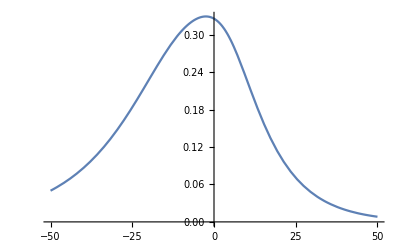

```mathematica
Plot[AmpIRS[t],{t,-50,50}]
```

```mathematica
MaxAmpIRS=FindMaxValue[{AmpIRS[t],-40<=t<=0},{t,-20}]
```

0.329343

```mathematica
tpIRS = First@FindArgMax[{AmpIRS[t],-40<=t<=0},{t,-20}]
```

-2.49293

```mathematica
Δtp = tpBoB-tpIRS
```

-13.5786

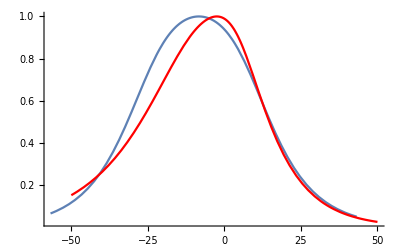

```mathematica
Show[Plot[AmpBoB[t+tfBoB]/MaxAmpBoB,{t,-50+Δtp/2,50+Δtp/2}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
PlotRange->All]
```

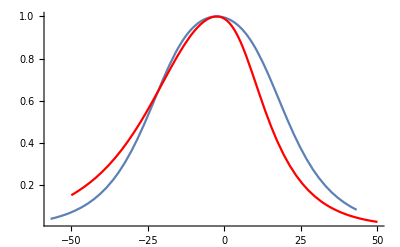

```mathematica
Show[Plot[AmpBoB[t+Δtp]/MaxAmpBoB,{t,-50+Δtp/2,50+Δtp/2}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
PlotRange->All]
```

```mathematica
hIRS[t_]:=AmpIRS[t]*Exp[-ⅈ*(ϕIRS)]
```

```mathematica
hIRSΔ[t_]:=AmpIRS[t]*Exp[-ⅈ*(ϕIRS+Δϕ)]
```

Let’s build the strains

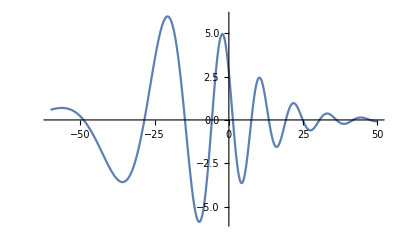

```mathematica
Plot[Re[hBoB[t]],{t,-60,50}]
```

```mathematica
MaxRehBoB = FindMaxValue[{Re[hBoB[t]],-40<=t<=-10},{t,-20}]
```

5.96775

```mathematica
MinRehBoB =FindMinValue[{Re[hBoB[t]],-20<=t<=0},{t,-10}]
```

-5.88028

```mathematica
thBoB = First@FindArgMax[{Re[hBoB[t]],-40<=t<=-10},{t,-20}]
```

-20.6272

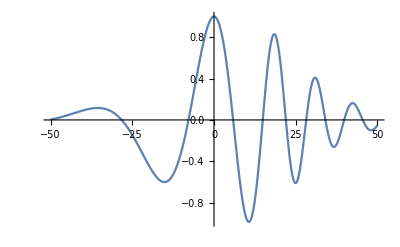

```mathematica
Plot[Re[hBoB[t+thBoB]]/MaxRehBoB,{t,-50,50}]
```

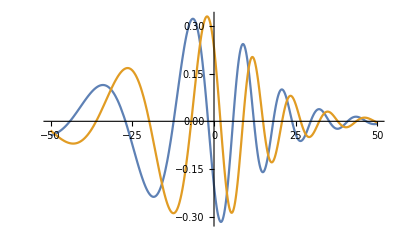

```mathematica
Plot[{Re[hIRS[t]],Re[hIRSΔ[t]]},{t,-50,50}]
```

```mathematica
MaxRehIRS = FindMaxValue[{Re[hIRS[t]],-20<=t<=0},{t,-10}]
```

0.321911

```mathematica
MinRehIRS = FindMinValue[{Re[hIRS[t]],-10<=t<=10},{t,0}]
```

-0.31591

```mathematica
MaxRehΔIRS = FindMaxValue[{Re[hIRSΔ[t]],-20<=t<=0},{t,-10}]
```

0.329267

```mathematica
MinRehΔIRS = FindMinValue[{Re[hIRSΔ[t]],-10<=t<=10},{t,0}]
```

-0.28727

```mathematica
thIRS = First@FindArgMax[{Re[hIRS[t]],-20<=t<=0},{t,-10}]
```

-6.45771

```mathematica
thΔIRS = First@FindArgMax[{Re[hIRSΔ[t]],-20<=t<=0},{t,-10}]
```

-2.11796

```mathematica
t0hIRSBoB = thBoB-thIRS
```

-14.1695

```mathematica
t0hIRSΔBoB = thBoB-thΔIRS
```

-18.5093

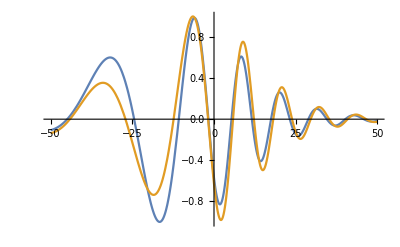

```mathematica
Plot[{-Re[hBoB[t-4]]/MaxRehBoB, Re[hIRS[t]]/MaxRehIRS},{t,-50,50}]
```

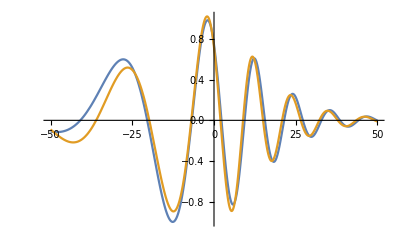

```mathematica
Plot[{-Re[hBoB[t-8]]/MaxRehBoB, Re[hIRSΔ[t]]/MaxRehIRS},{t,-50,50}]
```

```mathematica
tfBoB
```

-7.73417

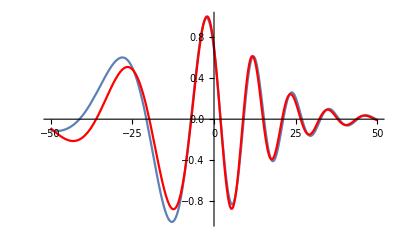

```mathematica
Show[Plot[Re[-hBoB[t+tfBoB]]/MaxRehBoB,{t,-50,50}],
Plot[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50},PlotStyle->Red],PlotRange->All]
```

Now we upload the SXS BBH:0180 data

```mathematica
(*SXS0180Data=Import["/Users/dillonbuskirk/dropbox/dillon/2022/BBH0180_22.dat","Table"]*)
```

```mathematica
SXS0180Data=Import["/Users/babiuc/BBH0180_22.dat","Table"]
```

{{-107.532,-0.00044193,-0.00471299},{-106.3,-0.000443996,-0.0047269},19291,{9758.27,-5.64872×10^-6,-0.0000188056},{9758.37,-5.65426×10^-6,-0.0000187994}}
 |  |  |  |

```mathematica
SXS0180DataTime=SXS0180Data[[All,1]];
```

```mathematica
ReSXS0180DataStrain=SXS0180Data[[All,2]];
```

```mathematica
MaxReSXS0180DataStrain=Max[ReSXS0180DataStrain]
```

0.390476

```mathematica
MinReSXS0746DataStrain=Min[ReSXS0180DataStrain]
```

-0.373573

```mathematica
ImSXS0180DataStrain=SXS0180Data[[All,3]];
```

```mathematica
MaxImSXS0180DataStrain=Max[ImSXS0180DataStrain]
```

0.374694

```mathematica
MinImSXS0180DataStrain=Min[ImSXS0180DataStrain]
```

-0.392091

```mathematica
AmpSXS0180DataStrain = Sqrt[ReSXS0180DataStrain^2+ImSXS0180DataStrain^2];
```

```mathematica
MaxAmpSXS0180DataStrain=Max[Abs[AmpSXS0180DataStrain]]
```

0.393661

```mathematica
Position[AmpSXS0180DataStrain ,_?(#>0.999999*MaxAmpSXS0180DataStrain&)]
```

{{16930}}

```mathematica
ReSXS0180DataStrainNorm = ReSXS0180DataStrain/MaxReSXS0180DataStrain;
ImSXS0180DataStrainNorm = ImSXS0180DataStrain/MaxImSXS0180DataStrain;
```

```mathematica
Position[ReSXS0180DataStrain ,_?(#>0.999999*MaxReSXS0180DataStrain&)]
```

{{16903}}

```mathematica
SXS0180DataTimeShift=SXS0180DataTime-SXS0180DataTime[[16930]];
```

```mathematica
hpReSXS0180DataShift=Transpose[{SXS0180DataTimeShift,+ReSXS0180DataStrainNorm}];
```

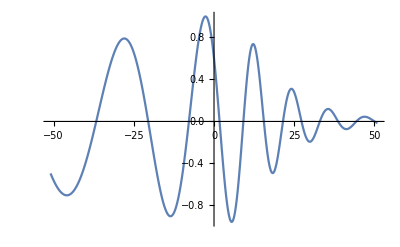

```mathematica
ListLinePlot[hpReSXS0180DataShift[[16420;;17440]]]
```

```mathematica
AmpSXS0180DataStrainNorm = AmpSXS0180DataStrain/MaxAmpSXS0180DataStrain;
```

```mathematica
AmpSXS0180DataShift=Transpose[{SXS0180DataTimeShift,AmpSXS0180DataStrainNorm }];
```

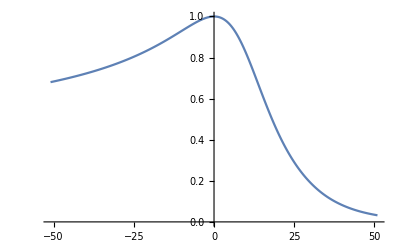

```mathematica
ListLinePlot[AmpSXS0180DataShift[[16420;;17440]]]
```

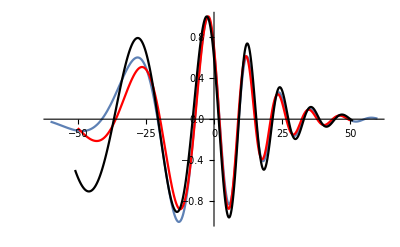

```mathematica
Show[Plot[-Re[hBoB[t+tfBoB]]/MaxRehBoB,{t,-60,60}],
Plot[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[hpReSXS0180DataShift[[16420;;17440]],PlotStyle->Black],
PlotRange->All]
```

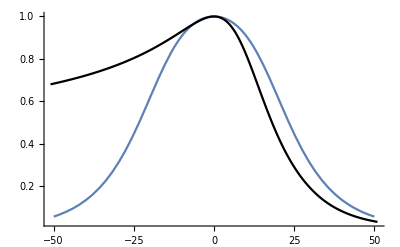

```mathematica
Show[Plot[AmpBoB[t+tpBoB]/MaxAmpBoB,{t,-50,50}],
ListLinePlot[AmpSXS0180DataShift[[16420;;17440]],PlotStyle->Black],PlotRange->All]
```

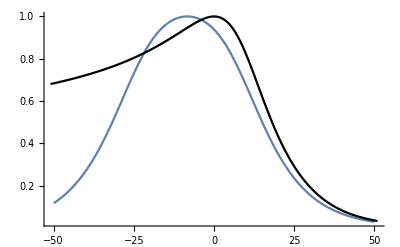

```mathematica
Show[Plot[AmpBoB[t+tfBoB]/MaxAmpBoB,{t,-50,50}],
ListLinePlot[AmpSXS0180DataShift[[16420;;17440]],PlotStyle->Black],PlotRange->All]
```

```mathematica
SXS0180DataTimeShiftIRS=SXS0180DataTime-SXS0180DataTime[[16930]] +tpIRS;
AmpSXS0180DataShiftIRS=Transpose[{SXS0180DataTimeShiftIRS,AmpSXS0180DataStrainNorm }];
```

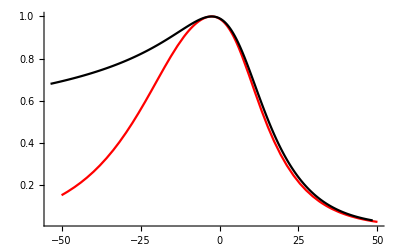

```mathematica
Show[
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[AmpSXS0180DataShiftIRS[[16420;;17440]],PlotStyle->Black],
PlotRange->All]
```

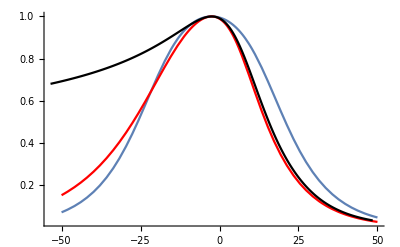

```mathematica
Show[Plot[AmpBoB[t+Δtp]/MaxAmpBoB,{t,-50,50}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[AmpSXS0180DataShiftIRS[[16420;;17440]],PlotStyle->Black],PlotRange->All]
```

```mathematica
ArgSXS= Flatten[ArcTan[ImSXS0180DataStrainNorm/ReSXS0180DataStrainNorm]];
```

Function taken from https://community.wolfram.com/groups/-/m/t/1340126

```mathematica
Unwrap[lst_List]:=Unwrap[lst,2Pi] (*phase jumps of 2Pi is the default because of trigonometric funtions*)
Unwrap[lst_List,Δ_]:=Unwrap[lst,Δ,Scaled[0.5]] (*default tolerance is half the phase jump Δ*)
Unwrap[lst_List,Δ_,tolerance_]:=Module[{tol,jumps},tol=If[Head[tolerance]===Scaled,Δ tolerance[[1]],tolerance];
jumps=Differences[lst];
jumps=-Sign[jumps]Unitize[Chop[Abs[jumps],tol]];
jumps=Δ Prepend[Accumulate[jumps],0];
jumps+lst]
```

```mathematica
unwrapArgSXS=Unwrap[ArgSXS,3];
```

```mathematica
unwrapArgSXSFiltered=MeanFilter[unwrapArgSXS,100];
```

```mathematica
ϕSXS=Transpose[{SXS0180DataTimeShift,Flatten[-unwrapArgSXS]}];
```

```mathematica
ϕSXSfiltered=Transpose[{SXS0180DataTimeShift,Flatten[-unwrapArgSXSFiltered]}];
```

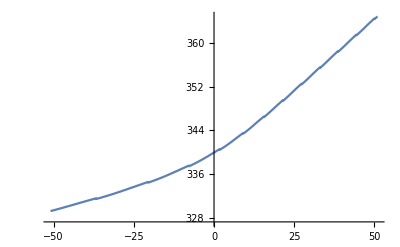

```mathematica
ListLinePlot[ϕSXS[[16420;;17440]]]
```

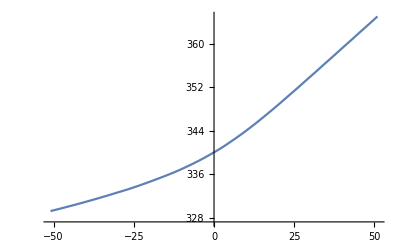

```mathematica
ListLinePlot[ϕSXSfiltered[[16420;;17440]]]
```

```mathematica
interpϕSXS=Interpolation[ϕSXS[[16420;;17440]],InterpolationOrder->4]
```

InterpolatingFunction[…]

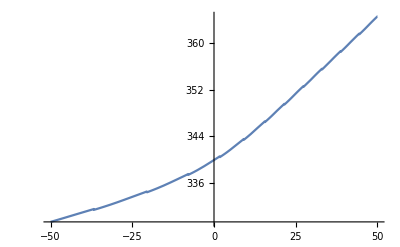

```mathematica
Show[Plot[interpϕSXS[t],{t,-50,50}]]
```

```mathematica
interpϕSXSfiltered=Interpolation[ϕSXSfiltered[[16420;;17440]],InterpolationOrder->4]
```

InterpolatingFunction[…]

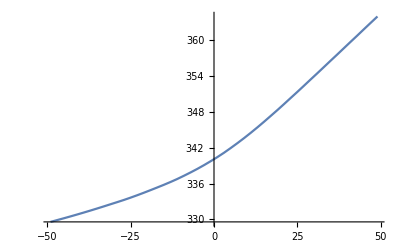

```mathematica
Show[Plot[interpϕSXSfiltered[t],{t,-49,49}]]
```

```mathematica
ΔϕSXSBoB =interpϕSXSfiltered[0]-Re[ϕBoB[tfBoB]]
```

333.004

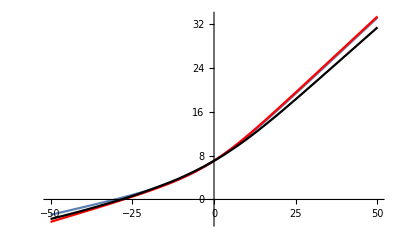

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

https://mathematica.stackexchange.com/questions/126302/how-to-get-a-smooth-derivative-graphic

```mathematica
dϕSXS=Differences[Last/@ϕSXSfiltered]
```

{0.0153185,0.01536,0.0154045,0.0154492,0.0154929,0.0155385,0.0155799,19281,0.0000848735,0.0000818043,0.0000785944,0.0000752584,0.000071814,0.0000682788}
 |  |  |  |

```mathematica
dϕSXS=dϕSXS/Differences[First/@ϕSXSfiltered]
```

{0.012432,0.0124657,0.0125018,0.0125381,0.0125735,0.0126105,0.0126441,19280,0.000877938,0.000848782,0.000818088,0.000785987,0.000752626,0.000718179,0.000682826}
 |  |  |  |

```mathematica
dϕSXSfiltered=MeanFilter[dϕSXS,100]
```

{0.0124714,0.0125445,0.0126168,0.0126901,0.0127646,0.0128371,0.0129095,19280,0.000704994,0.000700369,0.000695541,0.000690512,0.00068528,0.000679844,0.000674205}
 |  |  |  |

```mathematica
{dϕSXS,dϕSXSfiltered}=Transpose[{Most[First/@ϕSXSfiltered],#}]&/@{dϕSXS,dϕSXSfiltered}
```

{{{-9629.43,0.012432},{-9628.2,0.0124657},{-9626.97,0.0125018},19288,{236.168,0.000752626},{236.268,0.000718179},{236.368,0.000682826}},{1}}
 |  |  |  |

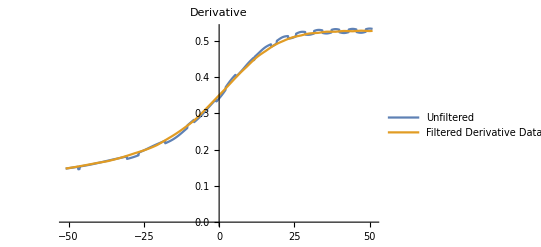

```mathematica
ListLinePlot[{dϕSXS[[16420;;17440]],dϕSXSfiltered[[16420;;17440]]},PlotStyle->{Thin,Thick},PlotLegends->{"Unfiltered","Filtered Derivative Data"},PlotLabel->"Derivative"]
```

```mathematica
interpωSXSfiltered=Interpolation[dϕSXSfiltered[[16420;;17440]],InterpolationOrder->4]
```

InterpolatingFunction[…]

```mathematica
interpωSXSfiltered[0]
```

0.350391

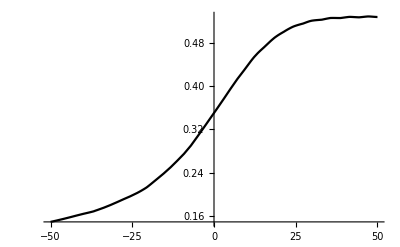

```mathematica
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->Black]
```

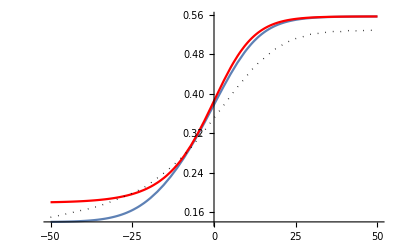

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[ωIRS[t],{t,-50,50},PlotStyle->Red],
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->{Black,Dotted, Thick}],
PlotRange->All]
```

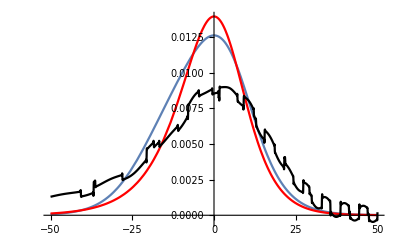

```mathematica
Show[Plot[ωBoB'[t+tfBoB],{t,-50,50}],
Plot[ωIRS'[t],{t,-50,50},PlotStyle->Red],
Plot[interpωSXSfiltered'[t],{t,-50,50},PlotStyle->{Black}],
PlotRange->All]
```

Plots for the paper

```mathematica
Show[Plot[-Re[hBoB[t+tfBoB]]/MaxRehBoB,{t,-60,60}],
Plot[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[hpReSXS0180DataShift[[16420;;17440]],PlotStyle->Black],
PlotRange->All]
```

-Graphics-

Fig. 2

```mathematica
Show[Plot[AmpBoB[t+Δtp]/MaxAmpBoB,{t,-50,50}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[AmpSXS0180DataShiftIRS[[16420;;17440]],PlotStyle->Black],PlotRange->All]
```

-Graphics-

Fig. 3

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

-Graphics-

Fig. 1

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[ωIRS[t],{t,-50,50},PlotStyle->Red],
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->{Black,Dotted, Thick}],
PlotRange->All]
```

-Graphics-

```mathematica
interpωSXSfiltered[50]
```

0.52751

```mathematica
ωBoB[50+tfBoB]
```

0.556342

Light Ring Location

```mathematica
rLR[χf_] := 2 m(1 + Cos[2/3 ArcCos[-χf]])
```

```mathematica
rLRp=rLR[χf]/.{ m->1}
rLRm=rLR[-χf]/.{ m->1}
rLR = Mean[List[rLRp,rLRm]]
```

2.03826

3.7126

2.87543

```mathematica
rLR0=rLR[0]/.{ m->1}
```

2.87543[0]

```mathematica
rLR0Mf=rLR[0]/.{ m->Mf}
```

2.87543[0]

```mathematica
rLR[χf]/.{ m->Mf}
```

2.87543[0.686527]

```mathematica
Tc =Simplify[ 5/256 a^4/(m1 m2 m)]
```

(0.078125 a^4)/m

```mathematica
Tcp = Simplify[Tc/.{m->1,a->rLRp}]
Tcm = Simplify[Tc/.{m->1,a->rLRm}]
```

1.34843

14.8424

```mathematica
Mean[List[Tcp,Tcm]]
```

8.09542

```mathematica
TLR = Simplify[Tc/.{m->1,a->rLR}]
```

5.34075

```mathematica
TLRMf = Simplify[Tc/.{m->Mf,a->rLR0Mf}]
```

0.0821289 (2.87543[0])^4

```mathematica
TLR0 = Simplify[Tc/.{m->1,a->rLR0}]
```

0.078125 (2.87543[0])^4

```mathematica
rLR0/6.328125
```

0.158025 2.87543[0]

```mathematica
tfBoB
```

-7.73417

```mathematica
tpBoB
```

-16.0715

```mathematica
ti-tfBoB
```

-30.3026

For the standard deviation plot

```mathematica
(*dataBoBr=Re[hBoB[t-trBoB/2]]/MaxAmpBoB;
dataBoB0=Re[hBoB[t-Δt0/2]]/MaxAmpBoB;
dataIRS=Re[hIRSΔ[t]]/MaxAmpIRS;
datamIRS=Re[-hIRS[t]]/MaxAmpIRS;
datamIRSΔ=Re[-hIRSΔ[t]]/MaxAmpIRS;*)
```

## Below is Tabulating for Python Plots

```mathematica
(*dt=0.01;*)
```

```mathematica
(*tArray=Table[t,{t,-50,50,dt}];*)
```

```mathematica
(*ωBoBTab=Table[ωBoB[t+tfBoB],{t,-50,50,dt}];*)
```

```mathematica
(*ωIRSTab=Table[ωIRS[t],{t,-50,50,dt}];*)
```

```mathematica
(*ωSXSTab=Table[interpωSXSfiltered[t],{t,-50,50,dt}];*)
```

```mathematica
(*ωBoBvsTimeTab=Partition[Riffle[tArray,ωBoBTab],2];*)
```

```mathematica
(*PrependTo[ωBoBvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
(*ωIRSvsTimeTab=Partition[Riffle[tArray,ωIRSTab],2];*)
```

```mathematica
(*PrependTo[ωIRSvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
(*ωSXSvsTimeTab=Partition[Riffle[tArray,ωSXSTab],2];*)
```

```mathematica
(*PrependTo[ωSXSvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/wBoB.txt", ωBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/wIRS.txt", ωIRSvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/wSXS.txt", ωSXSvsTimeTab]*)
```

```mathematica
(*ampBoBTab=Table[AmpBoB[t+Δtp]/MaxAmpBoB,{t,-50,50,dt}];*)
```

```mathematica
(*ampBoBvsTimeTab=Partition[Riffle[tArray,ampBoBTab],2];*)
```

```mathematica
(*PrependTo[ampBoBvsTimeTab, {"t(M)", "Amp"}];*)
```

```mathematica
(*ampIRSTab=Table[AmpIRS[t]/MaxAmpIRS,{t,-50,50,dt}];*)
```

```mathematica
(*ampIRSvsTimeTab=Partition[Riffle[tArray,ampIRSTab],2];*)
```

```mathematica
(*PrependTo[ampIRSvsTimeTab, {"t(M)", "Amp"}];*)
```

```mathematica
(*AmpSXS=PrependTo[AmpSXS0180DataShiftIRS[[16420;;17440]], {"t(M)", "Amp"}];*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/ampBoB.txt", ampBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/ampIRS.txt", ampIRSvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/ampSXS.txt", AmpSXS]*)
```

```mathematica
(*Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]*)
```

```mathematica
(*ϕBoBTab=Table[ϕBoB[t+tfBoB],{t,-50,50,dt}];*)
```

```mathematica
(*ϕIRSTab=Table[ϕIRS+Δϕ,{t,-50,50,dt}];*)
```

```mathematica
(*ϕSXSTab=Table[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50,dt}];*)
```

```mathematica
(*ϕBoBvsTimeTab=Partition[Riffle[tArray,ϕBoBTab],2];*)
```

```mathematica
(*PrependTo[ϕBoBvsTimeTab, {"t(M)", "ϕ(t)"}];*)
```

```mathematica
(*ϕIRSvsTimeTab=Partition[Riffle[tArray,ϕIRSTab],2];*)
```

```mathematica
(*PrependTo[ϕIRSvsTimeTab, {"t(M)", "ϕ(t)"}];*)
```

```mathematica
(*ϕSXSvsTimeTab=Partition[Riffle[tArray,ϕSXSTab],2];*)
```

```mathematica
(*PrependTo[ϕSXSvsTimeTab, {"t(M)", "ϕ(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/phiBoB.txt", ϕBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/phiIRS.txt", ϕIRSvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/phiSXS.txt", ϕSXSvsTimeTab]*)
```

```mathematica
(*"dropbox/dillon/2022/Data/phiSXS.txt"*)
```

```mathematica
(*Show[Plot[-Re[hBoB[t+tfBoB]]/MaxRehBoB,{t,-60,60}],
Plot[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[hpReSXS0180DataShift[[16420;;17440]],PlotStyle->Black],
PlotRange->All]*)
```

```mathematica
(*hBoBTab=Table[-Re[hBoB[t+tfBoB]]/MaxRehBoB,{t,-50,50,dt}];*)
```

```mathematica
(*hIRSTab=Table[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50,dt}];*)
```

```mathematica
(*hBoBvsTimeTab=Partition[Riffle[tArray,hBoBTab],2];*)
```

```mathematica
(*PrependTo[hBoBvsTimeTab, {"t(M)", "h(t)"}];*)
```

```mathematica
(*hIRSvsTimeTab=Partition[Riffle[tArray,hIRSTab],2];*)
```

```mathematica
(*PrependTo[hIRSvsTimeTab, {"t(M)", "h(t)"}];*)
```

```mathematica
(*hSXS=PrependTo[hpReSXS0180DataShift[[16420;;17440]], {"t(M)", "h(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/hBoB.txt", hBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/hIRS.txt", hIRSvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/2022/Data/hSXS.txt", hSXS]*)
```